### Mass Matrix - 1 Flavour Scenario for Fine-Cancellation Mechanism

```mathematica
t=0.1;W=2;K=8;y=01;v=0.173;
(* K is the number of sites, y is the coupling strength between SM neutrino and BSM fields, v is the Higgs vev/√2 W is the mass term (ϵ) and t is neighbouring coupling strength. *)
```

```mathematica
e1[t_,W_]:=RandomReal[{W,W},K]  (*Can be a random list*)
```

```mathematica
g = e1[t,W];
```

```mathematica
Ox = Table[0,{x,2K},{y,2K}];
```

```mathematica
i=1;While[i<K+1,{Ox[[i,i+K]] = W,Ox[[i+K,i]] = W };i++]
i=1;While[i<K,{Ox[[i+1,i+K]] = t,Ox[[i+K,i+1]]=t};i++]
i=1;While[i<K,{Ox[[i,i+1+K]] = t,Ox[[i+K+1,i]]=t};i++]
```

```mathematica
Ox
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0.1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.1 | 2 | 0.1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.1 | 2 | 0.1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.1 | 2 | 0.1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.1 | 2 | 0.1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.1 | 2 | 0.1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.1 | 2 | 0.1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.1 | 2
2 | 0.1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.1 | 2 | 0.1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.1 | 2 | 0.1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.1 | 2 | 0.1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.1 | 2 | 0.1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.1 | 2 | 0.1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.1 | 2 | 0.1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.1 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
ev1=Eigenvalues[Ox]
```

{-2.18794,2.18794,2.15321,-2.15321,2.1,-2.1,2.03473,-2.03473,-1.96527,1.96527,-1.9,1.9,1.84679,-1.84679,1.81206,-1.81206}

```mathematica
Eigenvectors[SetPrecision[Ox,25]];
```

```mathematica
Ox1 = Ox[[1;;K,K+1;;2K]]
```

(2 | 0.1 | 0 | 0 | 0 | 0 | 0 | 0
0.1 | 2 | 0.1 | 0 | 0 | 0 | 0 | 0
0 | 0.1 | 2 | 0.1 | 0 | 0 | 0 | 0
0 | 0 | 0.1 | 2 | 0.1 | 0 | 0 | 0
0 | 0 | 0 | 0.1 | 2 | 0.1 | 0 | 0
0 | 0 | 0 | 0 | 0.1 | 2 | 0.1 | 0
0 | 0 | 0 | 0 | 0 | 0.1 | 2 | 0.1
0 | 0 | 0 | 0 | 0 | 0 | 0.1 | 2)

```mathematica
Eigenvalues[Ox1]
```

{2.18794,2.15321,2.1,2.03473,1.96527,1.9,1.84679,1.81206}

```mathematica
Lam[x_]:=W(1+2Cos[x*π/(K+1)])
```

```mathematica
la = Table[Lam[i],{i,1,K}]
```

{2 (1+2 cos(π/9)),2 (1+2 cos((2 π)/9)),4,2 (1+2 sin(π/18)),2 (1-2 sin(π/18)),0,2 (1-2 cos((2 π)/9)),2 (1-2 cos(π/9))}

```mathematica
{ou,ow,ov}=SingularValueDecomposition[SetPrecision[Ox1,20]];
```

```mathematica
ow
```

(2.1879385241571816872 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2.1532088886237956155 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2.1000000000000000056 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2.0347296355333860717 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1.9652703644666139283 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1.8999999999999999944 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1.8467911113762043845 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.8120614758428183128)

```mathematica
L1 = ou[[1]];
Rn = ov[[-1]];
```

```mathematica
Massmat2 = Table[0,{i,1,K+1},{j,1,K+1}];
(* Dummy Matrix to store values of full Mass matrix. *)
```

```mathematica
k=1;While[k<K+1,{Massmat2[[k+1,k+1]] = ow[[k,k]] };k++]
i=1;While[i<K+1,{Massmat2[[1,1+i]] = v*y*L1[[i]],Massmat2[[1+i,1]]=v*y*Rn[[i]]};i++]
(* Full Mass matrix with eigenvectors of Ox1 matrix as basis. *)
```

```mathematica
Rationalize[Massmat2,10^(-15)](*Rationalizing the mass matrix*)
```

(0 | 1112859/39897769 | -1406092/26822941 | 1630803/23090377 | -2696171/33570370 | 2696171/33570370 | -1630803/23090377 | 1406092/26822941 | 1112859/39897769
1112859/39897769 | 77682195/35504743 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1406092/26822941 | 0 | 90971536/42249285 | 0 | 0 | 0 | 0 | 0 | 0
1630803/23090377 | 0 | 0 | 21/10 | 0 | 0 | 0 | 0 | 0
2696171/33570370 | 0 | 0 | 0 | 52682943/25891864 | 0 | 0 | 0 | 0
2696171/33570370 | 0 | 0 | 0 | 0 | 50884513/25891864 | 0 | 0 | 0
1630803/23090377 | 0 | 0 | 0 | 0 | 0 | 19/10 | 0 | 0
1406092/26822941 | 0 | 0 | 0 | 0 | 0 | 0 | 78025604/42249285 | 0
-1112859/39897769 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 64336777/35504743)

```mathematica
{um,wm,vm} = SingularValueDecomposition[SetPrecision[Massmat2,20]];
wm //Diagonal
```

{2.1883105472400114463,2.1545330800271667647,2.1024331263453921263,2.0379253355231124959,1.9685221017618693939,1.9025581781178380157,1.8482212077991895777,1.8124703894901543492,1.1809092369091270646×10^-11}

### 3 Flavour Scenario

```mathematica
y=0.1;v=0.173;t=0.5;p=y*v;W=10;K=8;
(* K is the number of sites, y is the coupling strength between SM neutrino and BSM fields, v is the Higgs vev/√2 W is the mass term (ϵ) and t is neighbouring coupling strength. *)
```

```mathematica
decon= Table[0,{x,K+1},{y,K+1}];
(* Dummy matrix to form mass matrix *)
```

```mathematica
i=1;While[i<K+1,{decon[[i+1,i+1]] = W };i++]
i=2;While[i<K+1,{decon[[i+1,i]] = f,decon[[i,i+1]]=f};i++]
decon2=decon;decon3=decon;
```

```mathematica
decon[[1,2]]=decon[[-1,1]]=07p;decon2[[1,2]]=decon2[[-1,1]]=7.06p;decon3[[1,2]]=decon3[[-1,1]]=1p;
(*3 Deconstruction Mass chains for 3 masses.*)
```

```mathematica
decon
```

(0 | 0.1211 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 10 | 0.1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.1 | 10 | 0.1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.1 | 10 | 0.1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.1 | 10 | 0.1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.1 | 10 | 0.1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.1 | 10 | 0.1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.1 | 10 | 0.1
0.1211 | 0 | 0 | 0 | 0 | 0 | 0 | 0.1 | 10)

```mathematica
{u1,m1,v1}=SingularValueDecomposition[SetPrecision[decon,20]];{u2,m2,v2}=SingularValueDecomposition[SetPrecision[decon2,20]];{u3,m3,v3}=SingularValueDecomposition[SetPrecision[decon3,20]];
```

```mathematica
m11 = m1[[-1,-1]]
m22 = m2[[-1,-1]]
m33 = m3[[-1,-1]](*Three Masses produced*)
```

1.4673328115109704846×10^-17

1.4925911232353542827×10^-17

2.994987081627310987×10^-19

```mathematica
(m22^2-m11^2)*10^(24)(*Mass squared differences Subscript[Δm^2, 21].*)
```

7.4762681424287319×10^-12

```mathematica
(m33^2-m11^2)*10^(24)(*Mass squared differences Subscript[Δm^2, 32].*)
```

-2.152168584974777789×10^-10

## Branching ratio for μ → e + γ,

```mathematica
brl=Table[0,{i,20},{j1,4}];ma1=Table[0,{i,20},{j1,4}];
fj = {1,0.5,0.2,0.1};
```

```mathematica
j1=1;
While[j1<5,{i1=1;
While[i1<21,{W=i1*1;K=8;y=0.1;v=0.173;f=fj[[j1]];p=y*v;
cw= Table[0,{x,K+1},{y,K+1}];
(* Dummy matrix to form clockwork mass matrix *)
i=1;While[i<K+1,{cw[[i+1,i+1]] = W };i++];
i=2;While[i<K+1,{cw[[i+1,i]] = f,cw[[i,i+1]]=f};i++];
cw2=cw;cw3=cw;
cw[[1,2]]=cw[[-1,1]]=01p;cw2[[1,2]]=cw2[[-1,1]]=3.1p;cw3[[1,2]]=cw3[[-1,1]]=7p;
{u1,m1,v1}=SingularValueDecomposition[SetPrecision[cw,30]];{u2,m2,v2}=SingularValueDecomposition[SetPrecision[cw2,30]];{u3,m3,v3}=SingularValueDecomposition[SetPrecision[cw3,30]];
Subscript[M, w] = 0.08;xe1 = Table[0,{i,1,K+1}];xe2 = Table[0,{i,1,K+1}];xe3 = Table[0,{i,1,K+1}];v=0.178;
i=1; While[i<K+2,{xe1[[i]] = SetPrecision[Power[m1[[i,i]]/Subscript[M, w],2],30]};i++];
i=1; While[i<K+2,{xe2[[i]] = SetPrecision[Power[m2[[i,i]]/Subscript[M, w],2],30]};i++];
i=1; While[i<K+2,{xe3[[i]] = SetPrecision[Power[m3[[i,i]]/Subscript[M, w],2],30]};i++];
Fe[x_]:= (10-43*x+78*x^2-49*x^3+4*x^4-18*x^3*Log[x])/(6*Power[1-x,4]);
Fev1 = Table[0,{i,1,K+1}];YM1 = Table[0,{i,1,K+1}];Fev2 = Table[0,{i,1,K+1}];YM2 = Table[0,{i,1,K+1}];Fev3 = Table[0,{i,1,K+1}];YM3 = Table[0,{i,1,K+1}];
i=1;While[i<K+2,{x=xe1[[i]],Fev1[[i]] = SetPrecision[Fe[x],30]};i++];
i=1;While[i<K+2,{YM1[[i]] =u1[[1,i]]*u1[[1,i]]};i++];
i=1;While[i<K+2,{x=xe2[[i]],Fev2[[i]] = SetPrecision[Fe[x],30]};i++];
i=1;While[i<K+2,{YM2[[i]] =u2[[1,i]]*u2[[1,i]]};i++];
i=1;While[i<K+2,{x=xe3[[i]],Fev3[[i]] = SetPrecision[Fe[x],30]};i++];
i=1;While[i<K+2,{YM3[[i]] =u3[[1,i]]*u3[[1,i]]};i++];
YF1 = Sum[YM1[[i]]*Fev1[[i]],{i,1,K+1}];
YF2 = Sum[YM2[[i]]*Fev2[[i]],{i,1,K+1}];
YF3 = Sum[YM3[[i]]*Fev3[[i]],{i,1,K+1}];
Vm = {-0.32667,0.66498,0.6716};
Ve={0.823,0.549538,-0.1438};
YF = {YF1,YF2,YF3};
YFF = Sum[YF[[i]]*Vm[[i]]*Conjugate[Ve[[i]]],{i,1,3}];
BR = N[3/(8*Pi*137)*YFF*Conjugate[YFF]]*v^0;brl[[i1,j1]]=BR;ma1[[i1,j1]]=m1[[-1,-1]]};i1++]};j1++]
```

```mathematica
brl
```

(0.0000323252 | 0.000144378 | 2.90097×10^-10 | 2.28876×10^-10
7.5612×10^-8 | 2.09275×10^-11 | 1.44943×10^-11 | 1.38543×10^-11
7.00629×10^-12 | 3.74264×10^-12 | 3.28962×10^-12 | 3.23314×10^-12
1.8014×10^-12 | 1.39502×10^-12 | 1.31231×10^-12 | 1.3013×10^-12
8.3466×10^-13 | 7.32032×10^-13 | 7.08127×10^-13 | 7.04855×10^-13
5.05001×10^-13 | 4.68425×10^-13 | 4.59337×10^-13 | 4.58075×10^-13
3.56029×10^-13 | 3.39951×10^-13 | 3.3581×10^-13 | 3.3523×10^-13
2.7646×10^-13 | 2.68318×10^-13 | 2.66175×10^-13 | 2.65873×10^-13
2.28972×10^-13 | 2.24409×10^-13 | 2.23191×10^-13 | 2.23019×10^-13
1.98309×10^-13 | 1.95551×10^-13 | 1.94807×10^-13 | 1.94701×10^-13
1.77317×10^-13 | 1.75549×10^-13 | 1.75069×10^-13 | 1.75001×10^-13
1.62286×10^-13 | 1.61099×10^-13 | 1.60774×10^-13 | 1.60728×10^-13
1.51133×10^-13 | 1.50305×10^-13 | 1.50078×10^-13 | 1.50046×10^-13
1.42617×10^-13 | 1.42021×10^-13 | 1.41857×10^-13 | 1.41833×10^-13
1.35957×10^-13 | 1.35517×10^-13 | 1.35396×10^-13 | 1.35379×10^-13
1.30646×10^-13 | 1.30314×10^-13 | 1.30222×10^-13 | 1.30209×10^-13
1.26338×10^-13 | 1.26082×10^-13 | 1.26011×10^-13 | 1.26001×10^-13
1.22793×10^-13 | 1.22593×10^-13 | 1.22537×10^-13 | 1.22529×10^-13
1.19839×10^-13 | 1.19679×10^-13 | 1.19635×10^-13 | 1.19629×10^-13
1.17349×10^-13 | 1.17221×10^-13 | 1.17186×10^-13 | 1.17181×10^-13)

```mathematica
ma1
```

(0.00704913811464231223195210351187 | 0.0000663091100368072987025181765594 | 5.15173505367517709742371516716×10^-9 | 3.2120330944169593692653042163×10^-11
0.0000332294018459488381555769455845 | 1.4761982395778824823273626348×10^-8 | 1.60638820559938256650110911996×10^-11 | 1.18972222071554612324068600565×10^-13
1.15818382227140631340259084016×10^-7 | 4.36233572773165558461639908619×10^-10 | 6.02436292281724838053884569672×10^-13 | 4.59717069181593873510459495026×10^-15
7.38150379944423799523684066586×10^-9 | 3.98965467291885265928697422222×10^-11 | 5.94894743938329944554560399932×10^-14 | 4.58675759485158255837166683839×10^-16
1.03068407998388631227980351588×10^-9 | 6.42596920310411952575400705472×10^-12 | 9.91771471851529789005996545567×10^-15 | 7.68322676671202464469120047584×10^-17
2.18122726192425967470788121344×10^-10 | 1.46211627460037481888387210748×10^-12 | 2.29864286586815668617927992662×10^-15 | 1.78535000730202196977499870368×10^-17
6.01368377328304531424390516004×10^-11 | 4.20449912779386587382354028086×10^-13 | 6.6834335332277286923675528315×10^-16 | 5.1990719115703298367165321317×10^-18
1.99485670630632781062462096398×10^-11 | 1.43251436365263596434532002616×10^-13 | 2.29341103204038459738707100016×10^-16 | 1.78585168868766222167404446776×10^-18
7.59149323935991864054839867633×10^-12 | 5.55089481504495625878684176253×10^-14 | 8.93023248740697743585647190569×10^-17 | 6.95866460154822849110311091419×10^-19
3.21301434523371722133212701554×10^-12 | 2.37961664808979142420255935745×10^-14 | 3.84164791739311493518054765099×10^-17 | 2.99498708162731098699361424744×10^-19
1.48033746795071054865306419457×10^-12 | 1.10672183836682984197402716884×10^-14 | 1.79128648616110612586861819055×10^-17 | 1.39701453100236428759222951725×10^-19
7.31062792807728411798992473385×10^-13 | 5.50454878143566941563803888481×10^-15 | 8.92680574296689467385130871838×10^-18 | 6.96389910528043202255289415906×10^-20
3.82542202545056703260006686674×10^-13 | 2.89628192254821657122234669277×10^-15 | 4.70407633049638844029438843458×10^-18 | 3.67049399835113874441708158876×10^-20
2.10225934417830058868922421815×10^-13 | 1.59860675812446991990587304361×10^-15 | 2.59954787145741165000838050518×10^-18 | 2.02872122758629035270539643115×10^-20
1.20491156976496804159317119815×10^-13 | 9.19463588789154760471009687465×10^-16 | 1.49662195278188988338947443315×10^-18 | 1.16814479456493022944047590655×10^-20
7.16259723783167481726084275302×10^-14 | 5.48143941821924186914650939256×10^-16 | 8.92928977571944702955027202336×10^-19 | 6.97028596425300182111924013721×10^-21
4.39611832587819385763099499557×10^-14 | 3.37227760455650075642008279617×10^-16 | 5.49706919502693040514896161735×10^-19 | 4.29146507818747691119299731266×10^-21
2.77545517080207350868226136652×10^-14 | 2.13329040641456776284107957902×10^-16 | 3.47934194627631795548575576773×10^-19 | 2.7164742786545658206680582974×10^-21
1.79686767770195844143737392581×10^-14 | 1.38344008549095968756766695621×10^-16 | 2.25740720928255550518753993067×10^-19 | 1.76257357164230180478622188924×10^-21
1.18981101497475897352377523343×10^-14 | 9.17368023157940882488530131723×10^-17 | 1.49749690320620478866403479694×10^-19 | 1.16930530515037336988131807362×10^-21)

```mathematica
e1 = 4.2*10^(-13);
exp = Table[e1,{i,20}];
fut1 = 4*10^(-14);
futexp = Table[fut1,{i,20}];
```

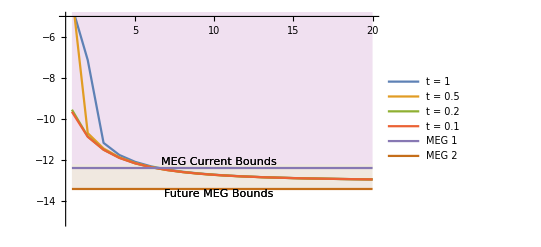
-Graphics-Log_10 of BRϵ (TeV)

```mathematica
Labeled[ListLinePlot[{Log10[brl[[;;,1]]],Log10[brl[[;;,2]]],Log10[brl[[;;,3]]],Log10[brl[[;;,4]]],Log10[exp],Log10[futexp]},PlotLegends->LineLegend[{"t = 1","t = 0.5","t = 0.2","t = 0.1","MEG 1","MEG 2"},LegendMarkerSize->10,LegendFunction->Frame],LabelStyle->{FontSize->10,FontWeight->Bold},PlotRange->{All,{-15,-5}},RotateLabel->True,Filling->{{5->{1,LightPurple}},{6->{-12.2,LightBrown}}},Epilog->{Text["Future MEG Bounds",Scaled[{0.5,0.15}]] ,Text["Future MEG Bounds",Scaled[{0.5,0.15}]] ,Text["MEG Current Bounds",Scaled[{0.5,0.3}]] ,Text["MEG Current Bounds",Scaled[{0.5,0.3}]] }],{"\!\(\*SubscriptBox[\(Log\), \(10\)]\) of BR","ϵ (TeV)"},{Left,Top},RotateLabel->True]
```

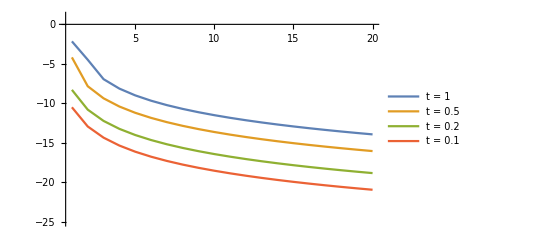
-Graphics-Log_10 of Smallest Mass in TeVn

```mathematica
Labeled[ListLinePlot[{Log10[ma1[[;;,1]]],Log10[ma1[[;;,2]]],Log10[ma1[[;;,3]]],Log10[ma1[[;;,4]]]},PlotLegends->LineLegend[{"t = 1","t = 0.5","t = 0.2","t = 0.1"},LegendMarkerSize->10,LegendFunction->Frame],LabelStyle->{FontSize->10,FontWeight->Bold},PlotRange->{All,{-25,1}},RotateLabel->True],{"Log_10 of Smallest Mass in TeV","n "},{Left,Top},RotateLabel->True]
```

```mathematica
PMNS = {{0.823,0.548,−0.087+0.120 * I},{−0.323+0.073 * I,0.601+0.049 *I,0.725},{0.456+0.068 *I,−0.575+0.045 *I,0.672}}
```

(0.823 | 0.548 | -0.087+0.12 ⅈ
-0.323+0.073 ⅈ | 0.601+0.049 ⅈ | 0.725
0.456+0.068 ⅈ | -0.575+0.045 ⅈ | 0.672)

```mathematica
PMNS[[1]].Conjugate[PMNS[[2]]]
```

0.000444+0.000069 ⅈ

```mathematica
Vm = {-0.32669184061566553,0.6650006626125635,0.6716};
Ve={0.823,0.5495384972865869,-0.1438};
```

```mathematica
Vm = {-0.32667,0.66498,0.6716};
Ve={0.823,0.549538,-0.1438};
```

```mathematica
Vm.Vm
Vm.Ve
Ve.Ve
```

0.999958

6.28924×10^-6

0.999999